```mathematica
golfshots={66,67,67,68,68,68,68,69,69,69,69,70,70,71,71,72,73,75}
```

{66,67,67,68,68,68,68,69,69,69,69,70,70,71,71,72,73,75}

```mathematica
N[golfshots-Mean[golfshots]]
```

{-3.44444,-2.44444,-2.44444,-1.44444,-1.44444,-1.44444,-1.44444,-0.444444,-0.444444,-0.444444,-0.444444,0.555556,0.555556,1.55556,1.55556,2.55556,3.55556,5.55556}

```mathematica
{-3.4444444444444446,-2.4444444444444446,-2.4444444444444446,-1.4444444444444444,-1.4444444444444444,-1.4444444444444444,-1.4444444444444444,-0.4444444444444444,-0.4444444444444444,-0.4444444444444444,-0.4444444444444444,0.5555555555555556,0.5555555555555556,1.5555555555555556,1.5555555555555556,2.5555555555555554,3.5555555555555554,5.555555555555555}
```

{-3.44444,-2.44444,-2.44444,-1.44444,-1.44444,-1.44444,-1.44444,-0.444444,-0.444444,-0.444444,-0.444444,0.555556,0.555556,1.55556,1.55556,2.55556,3.55556,5.55556}

```mathematica
N[Total[(golfshots-Mean[golfshots])^2]/(Length[golfshots]-1)]
```

5.20261

```mathematica
N[Variance[golfshots]]
```

5.20261

```mathematica
N[Sqrt[Total[(golfshots-Mean[golfshots])^2]/(Length[golfshots]-1)]]
```

2.28092

```mathematica
N[StandardDeviation[golfshots]]
```

2.28092

```mathematica
onlyone={66,69}
```

{66,69}

```mathematica
N[Mean[onlyone]]
```

67.5

```mathematica
N[onlyone-Mean[onlyone]]
```

{-1.5,1.5}

```mathematica
N[(onlyone-Mean[onlyone])^2]
```

{2.25,2.25}

```mathematica
N[Total[(onlyone-Mean[onlyone])^2]]
```

4.5

Era por causa do -1...

```mathematica
N[Total[(onlyone-Mean[onlyone])^2]/(Length[onlyone]-1)]
```

4.5

```mathematica
N[Variance[onlyone]]
```

4.5

### Amostragem

Dados: temperatura horária em dias randômicos de Julho e Agosto/2018.

```mathematica
ts:=WeatherData[Entity["City",{"SaoPaulo","SaoPaulo","Brazil"}],"Temperature",{{2018,7,1,0}, {2018,7,1,23}}]
```

```mathematica
ts["Path"]
```

{{3739392000,19 °C},{3739395600,18 °C},{3739399200,16 °C},{3739424400,13 °C},{3739428000,13 °C},{3739431600,13 °C},{3739435200,18 °C},{3739438800,19 °C},{3739442400,21 °C},{3739446000,23 °C},{3739449600,25 °C},{3739453200,25 °C},{3739456800,26 °C},{3739460400,26 °C},{3739464000,25 °C},{3739467600,21 °C},{3739471200,23 °C},{3739474800,20 °C}}

```mathematica
qm=QuantityMagnitude[ts["Values"]]
```

{19,18,16,13,13,13,18,19,21,23,25,25,26,26,25,21,23,20}

```mathematica
Head[qm]
```

List

```mathematica
qm[[1]]
```

19

### Plots dinâmicos

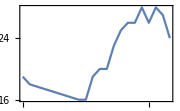

```mathematica
DateListPlot[WeatherData[Entity["City",{"SaoPaulo","SaoPaulo","Brazil"}],"Temperature",Today],ImageSize->Small]
```

### Exemplo do MatLab

```mathematica
v={102,96.8,97,92.5,95,93,99.4,99.8,105.5}
```

{102,96.8,97,92.5,95,93,99.4,99.8,105.5}

360 significa dividir todos os valores por 360. Para obter uma escala de 0 a 1 (frequência relativa).

```mathematica
t={97.,130.,167.5,187.5,218.,247.5,285.,315.,337.5}
ListPlot[t,Joined->True,Mesh->All,LabelingFunction->(#1&),PlotLabel->"Time orig",ImageSize->Small]
t2=t/360
ListPlot[t2,Joined->True,Mesh->All,LabelingFunction->(#1&),PlotLabel->"Time rel",ImageSize->Small]
```

{97.,130.,167.5,187.5,218.,247.5,285.,315.,337.5}

-Graphics-

{0.269444,0.361111,0.465278,0.520833,0.605556,0.6875,0.791667,0.875,0.9375}

-Graphics-

Média dos valores.

```mathematica
Mean[v]
```

97.8889

Std. deviation do tempo.

82.8064

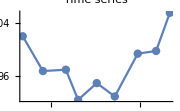

```mathematica
StandardDeviation[t]
ListPlot[{TimeSeries[v,{t2}]},Joined->True,Mesh->All,PlotLabel->"Time series",ImageSize->Small]
```

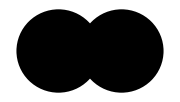

```mathematica
Region[BooleanRegion[Or,{Disk[{0,0},1],Disk[{1.5,0},1]}],ImageSize->Small]
```

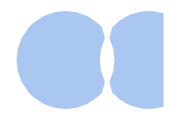

```mathematica
Region[RegionSymmetricDifference[Disk[{0,0},1],Disk[{1.7,0},1]],ImageSize->Small]
```

## Inferência estatística

1Estimação de parâmetros; testes de hipóteses; e predição.

Estimação

Estimando um parâmetro da população.
Parâmetro: uma constante desconhecida (letras gregas).
Hat (^) acima do nome do parâmetro: estimativa, ao invés de representar o valor verdadeiro na população.
A estimação de parâmetro busca encontrar um intervalo de valores apropriados para representar um parâmetro desconhecido.
A largura do intervalo representa a precisão do experimento: menos largo, mais preciso; mais largo, menos preciso.
Alargar um intervalo com um grau de confiança x aumenta o grau de confiança. Diminuir o intervalo diminui o grau de confiança. Há um equilíbrio entre “quanta confiança” e “quão estreito” o intervalo queremos obter.

Variação estocástica (randômica): sempre presente, mas a ser reduzida o máximo possível no modelo pela introdução de variáveis que expliquem as variações de outra forma.

Exemplo p. 25.

```mathematica
Clear[s1,s2]
s1={177,169,170,167,176,174,170,174,176,168};
s2={173,174,171,173,170,172,174,170,172,172};
```

```mathematica
{N[Mean[s1]],N[Mean[s2]]}
```

{172.1,172.1}

São duas amostras retiradas de populações diferentes.
As médias são iguais, mas...

```mathematica
{N[Total[(s1-Mean[s1])^2]/(Length[s1]-1)],
N[Total[(s2-Mean[s2])^2]/(Length[s2]-1)]}
```

{13.6556,2.1}

```mathematica
{N[Variance[s1]],N[Variance[s2]]}
```

{13.6556,2.1}

As variâncias são muito diferentes. O desvio padrão é na unidade dos dados, vamos calcular.

```mathematica
{Sqrt[N[Total[(s1-Mean[s1])^2]/(Length[s1]-1)]],
Sqrt[N[Total[(s2-Mean[s2])^2]/(Length[s2]-1)]]}
```

{3.69534,1.44914}

```mathematica
{N[StandardDeviation[s1]],N[StandardDeviation[s2]]}
```

{3.69534,1.44914}

Mesmo assim, da primeira amostra é quase o dobro. Portanto a “confiança básica” da primeira amostra é menor que a da segunda amostra.

Resultados antecipados:
Sobre a estimativa da média nas populações.
Tomando um intervalo, p.e., (171.1,173.1).
Através da amostra 1, podemos ter 95% de confiança que a média está neste intervalo na população 1 (de onde a amostra veio).
Na amostra 2, porém, a variância é significativamente maior. Isto reduz o grau de confiança de que a média na população 2 está dentro do mesmo intervalo, mesmo a média sendo igual nas duas amostras. O grau de confiança para o mesmo intervalo na população 2 é de 58%. Para aumentar o grau de confiança, p.e. para o mesmo da população 1, 95%, seria necessário expandir o intervalo (acompanhando a variância), para (169.5,174.7).
A diferença nos desvios padrão (que são na mesma unidade destes intervalos) é de 2.2462; a diferença nos intervalos é de 3.2.

```mathematica
N[StandardDeviation[s2]-StandardDeviation[s1]]
```

-2.2462

```mathematica
(173.1-171.1)-(174.7-169.5)
```

-3.2

```mathematica
Clear[sb1,sb2]
sb1={{177,27.9},{169,24.2},{170,25.2},{167,26.0},{176,26.4},{174,26.8},{170,26.9},{174,28.1},{176,29.0},{168,25.3}};
sb2={{169,27.4},{162,23.9},{157,25.0},{164,26.2},{164,26.3},{163,27.1},{161,27.2},{171,27.6},{171,28.2},{166,26.0}};
```

Plotar os primeiros como x e os segundos como y.

```mathematica
{sb1[[All,1]],sb1[[All,2]],sb2[[All,1]],sb2[[All,2]]}
```

{{177,169,170,167,176,174,170,174,176,168},{27.9,24.2,25.2,26.,26.4,26.8,26.9,28.1,29.,25.3},{169,162,157,164,164,163,161,171,171,166},{27.4,23.9,25.,26.2,26.3,27.1,27.2,27.6,28.2,26.}}

Inverter x com y para este gráfico.

```mathematica
{MatrixForm[sb1],MatrixForm[sb2]}
```

{(177 | 27.9
169 | 24.2
170 | 25.2
167 | 26.
176 | 26.4
174 | 26.8
170 | 26.9
174 | 28.1
176 | 29.
168 | 25.3),(169 | 27.4
162 | 23.9
157 | 25.
164 | 26.2
164 | 26.3
163 | 27.1
161 | 27.2
171 | 27.6
171 | 28.2
166 | 26.)}

```mathematica
{MatrixForm[Table[sb1[[i]][[
Which[j==1,2,j==2,1]
]],{i,10},{j,2}]],
MatrixForm[Table[sb2[[i]][[
Which[j==1,2,j==2,1]
]],{i,10},{j,2}]]}
```

{(27.9 | 177
24.2 | 169
25.2 | 170
26. | 167
26.4 | 176
26.8 | 174
26.9 | 170
28.1 | 174
29. | 176
25.3 | 168),(27.4 | 169
23.9 | 162
25. | 157
26.2 | 164
26.3 | 164
27.1 | 163
27.2 | 161
27.6 | 171
28.2 | 171
26. | 166)}

```mathematica
Clear[sb1inv,sb2inv]
sb1inv=Table[sb1[[i]][[
	Which[j==1,2,j==2,1]
]],{i,10},{j,2}];
sb2inv=Table[sb2[[i]][[
	Which[j==1,2,j==2,1]
]],{i,10},{j,2}];
```

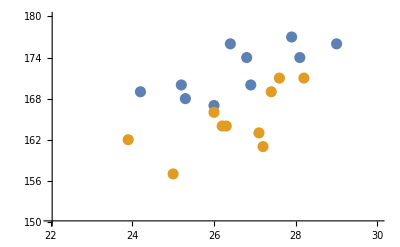

```mathematica
ListPlot[{sb1inv,sb2inv},PlotRange->{{22,30},{150,180}},PlotStyle->PointSize[0.02]]
```

Saber se sb1 e sb2 diferem na população. O grau de confiança que as médias na população diferem por entre 3.4 e 11.2, ou seja, que o intervalo da diferença das médias é até (3.4,11.2) é 95%.

Em ambos os exemplos, estamos com duas populações diferentes (embora no segundo seja um experimento/condição diferente na segunda população). No primeiro, estamos estimando médias para duas populações diferentes e comparando graus de confiança e intervalos. No segundo, estamos estimando a diferença entre as médias.

Exemplo do ponto crítico: ao aumentar a confiança da diferença entre as médias para 99%, o intervalo cresce para (2.0,12.6). Ao aumentar para 99.9%, o intervalo aceitável entre as médias chega no limiar inferior a 0: (0, 14.5). Neste ponto, a diferença poderia concebivelmente não existir e anulou-se a hipótese que um medicamento seria sempre superior ao outro. Aumentando mais a confiança, 99.91%, aceita-se a hipótese que o segundo medicamento possa (embora com chance remota) ser melhor que o primeiro.

O teste da hipótese que o segundo medicamento é sempre melhor que o primeiro é encontrar o valor que determina essa condição e calcular o intervalo que termina neste valor e o seu respectivo grau de confiança.
Por exemplo: a diferença entre as médias ser ≥0 (em favor de B). Ela é ≥0 em um intervalo de médias (0, 14.5) e para este intervalo o nível de confiança é 99.9%. Quanto maior o intervalo de confiança neste caso, mais “convincente” a hipótese.
Portanto este é um caminho, achar o “valor crítico” e testar a hipótese.
A “significância estatística” está em 95% de confiança (resultado “estatisticamente significante”).
P-value: 1-c/100: grau de confiança 95, p-value 0.05.
Então pode ser reportado o intervalo de confiança resultante, ou o grau de confiança deste intervalo.

Testes de hipóteses

Tomar um valor para o parâmetro e verificar se ele é “razoável”: aceito ou rejeitado.
Geralmente, como há n valores inclusos em uma estimativa com um certo grau de confiança, um valor de teste de hipótese tem um significado especial (maior que apenas estar em um intervalo) — valores críticos. Geralmente um valor contribuído por uma teoria. Teste com valor específico sem significado é irrelevante — sendo os intervalos preferíveis neste caso.

### Likelihood

Qual a probabilidade de um valor de parâmetro ser x em uma distribuição. Por exemplo, a distribuição “gerada” por um valor específico de um (outro) parâmetro.

Cada distribuição tem uma probabilidade para cada valor. Encontrar a distribuição que tem um valor x com probabilidade y?
Likelihood function: a função com todos os possíveis valores do parâmetro em todas as possíveis distribuições? (Para identificar valores específicos.)

Match de distribuição × dados (“fit” de distribuição a dados). Qual a distribuição que melhor se “encaixa” nos dados? Em dois passos: 1) a média; 2) o desvio padrão (os dois parâmetros que “descrevem” a distribuição normal). Ou seja, primeiro ajustar o centro, depois a “agudez”.

No cálculo das probabilidades, alteramos a “posição” para obter a probabilidade (área) dada uma distribuição (média, desvio padrão).
No cálculo dos “likelihoods”, alteramos a distribuição para obter, em uma posição, a probabilidade (valor de y).2

Notações:
pr(dados | distribuição) e 
L (distribuição | dados), respectivamente.

1	Diggle, Chetwynd. Statistics and Scientific Method - An Introduction for Students and Researchers. 2011 Oxford University Press

2	StatQuest: Probability vs Likelihood https://www.youtube.com/watch?v=pYxNSUDSFH4